# Data science and Machine Learning II - Green Bonds Project

A bond classifier to foster sustainable finance
Authors: Evangelia Nteventzi, Massimo Poretti and Filippo Trapanese

This project has been developed by three students enrolled in the course of Data Science and Machine Learning II which is the foundation stone of the Master’ s program in Sustainable Management and Technology jointly delivered by EPFL, IMD Business School and HEC Lausanne. The aim of this project is to implement the notions learned during the course while enhancing sustainability.

## Introduction

### Context

Green bonds are debt instruments issued by companies, governments and other organisations to raise capital for projects that have environmental benefits. Despite their incredible success in the recent years, green bonds still suffer from lack of standards. The International Capital Market Association is a global market initiative that promotes the development of the international capital and securities markets and it is currently focusing on green bonds. To shed light on this new bond category, a collection of voluntary frameworks, called the Principles has been created. The Principles outline best practices when issuing bonds serving social and/or environmental  purposes through global guidelines and recommendations that promote transparency and disclosure, thereby underpinning the integrity of the market.. The Principles  also raise awareness of the importance of environmental and social impact among financial market participants, which ultimately aims to attract more capital to support sustainable development.

To this extent, ICMA developed four Product Standards - principles - that go beyond the mere classification of green bonds and more accurately classify the issuance of debt securities for environmental or sustainable purposes  according to four different categories: Green Bonds, Social Bonds, Sustainability Bonds, and Sustainability-Linked Bonds. 

-	Green Bonds are bonds that are issued to raise capital for projects that have environmental benefits. These projects may include renewable energy, sustainable agriculture, clean transportation, and other initiatives that aim to reduce greenhouse gas emissions and protect the environment.

-	Social Bonds are bonds that are issued to raise capital for projects that have social benefits. These projects may include affordable housing, education, healthcare, and other initiatives that aim to improve the wellbeing of individuals and communities.

-	Sustainability Bonds are bonds that are issued to raise capital for projects that have both environmental and social benefits. These projects may include initiatives 	that promote sustainable development and address both environmental and social challenges.

-	Sustainability-Linked Bonds are bonds whose terms are linked to the issuer’s sustainability performance. For example, the interest rate on these bonds may be linked to the issuer’s progress in meeting certain environmental or social targets.

### The project in brief

In this project we explore Natural Language Processing techniques to build an accurate classifier that could predict the bond’s membership  in one of the four Principles. Moreover, since many of the bonds issued are linked with Sustainable Development Goals (SDGs) we provide a practical interface which allows the user to select the SDGs  they are more interested in, and as a result the bonds and the corresponding reports will be displayed in a dashboard. By offering a systematic tool that could predict the class of a bond according to the four ICMA Principles and an additional  dashboard for SDGs, we aim  to support investors in their decision-making,, foster sustainable finance and the advancement of SDG frameworks.

## Data import

Our data comprises of bond’s reports and fact sheets disclosed by companies upon the issuance of the bond, which is then labeled by ICMA  according to one of the four Principles. This information is available at this ICMA link.. In order to retrieve this information in a more adapted format to perform classification algorithms, we created a Python notebook (available on the GitHub folder) which extracts the reports directly from the original source present in the Excel file “ICMA-Sustainable-Bonds-Database-151022”. In this Section we first establish a local directory with all the files needed to perform our classifications, namely 761 for Green Bonds, 136 for Social Bonds, 233 for Sustainability Bonds and 79 for Sustainability-Linked Bonds. On the GitHub  directory only few reports are available due to storage constraints.Then, we extract the text from all the reports and we encode it as ASCII  to avoid problems that can arise from the different encoding of the files. Finally, we start to clean our data by lowering all cases and deleting stopwords.

### Local Directory

```mathematica
(* We retrieve the same number of bond reports from the local repository. Since there are fewer documents for sustainability-linked bonds, our sample will be limited to 78 report for each class*)
localdir = "C:\\Users\\massi\\Documents\\Università\\MASTER_EPFL\\Semester_3\\machine Learning\\Local_Green_Bonds\\files";
localreportsPath =FileNameJoin[{localdir,""}];
localfoldersPath = FileNames[All,localreportsPath];
localpdfPath = Map[FileNames[All,#]&,localfoldersPath];
localfileMaxNumber = Map[Length,localpdfPath]//Min;
SeedRandom[1234];
randomSample = Map[RandomSample[#,localfileMaxNumber]&,localpdfPath];
Map[Length,randomSample]
```

{78,78,78,78}

### Github Directory

```mathematica
(* Some reports are available on the Github page as examples since the maximum size of the project cannot exceed 200MB *)
dir = NotebookDirectory[];
reportsPath =FileNameJoin[{dir,"training_reports"}];
foldersPath = FileNames[All,reportsPath];
pdfPath = Map[FileNames[All,#]&,foldersPath];
```

```mathematica
(* the line of code below substitutes the repository directory with the local directory to use more pdfs*)
pdfPath = randomSample;
```

```mathematica
fileMaxNumber = Length[pdfPath[[1]]]
labelsList = {"green","social", "sustainability","sustainability related"};
(* this is how we create an association between documents and label*)
pdfClassification = AssociationThread[labelsList->pdfPath];
```

78

### Text Extraction

```mathematica
(* There are often encoding problems coming from different files, so we specify ASCII encoding to mitigate against this issue*)
ImportPlainText[label_,textNumber_]:=ToString[Import[pdfClassification[label][[textNumber]], "Plaintext"],CharacterEncoding->"ASCII"];
```

```mathematica
(* This is an example of how to retrieve a text given the label*)
pdfGreen = ImportPlainText["green",1];
pdfSocial = ImportPlainText["social",1];
```

```mathematica
(* We transform our data into a dataset after the deletion of stopwords and making all text lower case*)
ManageFullText[label_,textNumber_]:=Dataset[{<|"text"->ToLowerCase[DeleteStopwords[ImportPlainText[label,textNumber]]], "label"-> label|>}]
```

```mathematica
(* This takes around 5minutes and gives as result the complete dataset labeled with full text in "text" column *)
FullTextLabeledDataset =ManageFullText["green",1] ;
For[textNumber=1,textNumber<fileMaxNumber+1,textNumber++,For[label =1,label<5,label++,FullTextLabeledDataset=Join[FullTextLabeledDataset, ManageFullText[labelsList[[label]],textNumber]]]]
FullTextLabeledDataset = FullTextLabeledDataset[2;;All];
```

## Machine Learning

In this section we test different machine learning methods (Logistic Regression, K-Nearest Neighbours, etc. ) on different models (full text, sentences, words, etc.). The question we want to answer is: which is the most accurate algorithm  and on which type of model  does it perform the best? 
In the first three models, we want to predict the membership to one of the four Principles by using 1) the full text of the reports, 2) then splitting the text into sentences and finally, 3) into words.  At each step we clean the data differently in order to not loose precious information. For instance, when we analyse words we only delete all the words the include some strange symbols  (e.g., @, ☐, %). 
Next, in Model 4  we want to explore how SDGs could predict the membership to one of the Principles. To do so, we first extract SDGs from the texts by splitting them first in sentences and then finding the sentences that contain the word “sdg”, and then we use both words and SDGs together to predict the category.
In Model 5 we perform a deeper data cleaning and we run again the algorithm while in Model 6 we investigate Neural Networks.

### Methods

We start by applying the usual ML algorithms to classify the label knowing the full text

```mathematica
(* We create a ist to store the results *)
LogisticRegResults = {};
(* Logistic regression *)
LogisticReg[training_,test_]:=Module[{cLog=Classify[training->"label",Method->"LogisticRegression",ValidationSet->Automatic]},
cLogMeasurementsTest = ClassifierMeasurements[cLog, test];LogisticRegResults =Append[LogisticRegResults,cLogMeasurementsTest["Accuracy"]];cLogMeasurementsTest]
```

```mathematica
(* K-Nearest Neighbours *)
KNNResults = {};
KNN[training_,test_]:= Module[{cKNN =Classify[training -> "label", Method -> {"NearestNeighbors", "NeighborsNumber" -> #},ValidationSet->Automatic] & /@ Range[10]},
cKNNMeasurementsTest = ClassifierMeasurements[#, test] & /@ cKNN;
keyOptTest = Keys[Sort[<|#->cKNNMeasurementsTest[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cKNNAccTest=cKNNMeasurementsTest[[keyOptTest]];
KNNResults =Append[KNNResults,cKNNAccTest["Accuracy"]];
cKNNBest = cKNN[[keyOptTest]];cKNNAccTest]
```

```mathematica
(* Decision Tree *)
DecisionTreeResults={};
DecisionTree[training_,test_]:= Module[{cTree=Classify[training-> "label", Method -> {"DecisionTree", "FeatureFraction" -> #}]&/@ (Range[10]/(ncol-1))},
cTreeMeasurementsTest = ClassifierMeasurements[#, test] & /@ cTree;
keyOptTestTree = Keys[Sort[<|#->cTreeMeasurementsTest[[#]]["Accuracy"]&/@Range[10]|>]][[-1]];
cTreeBest = cTree[[keyOptTestTree]];
cTreeAccTestBest = ClassifierMeasurements[cTreeBest, test];
DecisionTreeResults =Append[DecisionTreeResults,cTreeAccTestBest ["Accuracy"]];cTreeAccTestBest]
```

```mathematica
(* Random Forest *)
RandomForestResults = {};
RandomForest[training_,test_]:=Module[{cRandFor=Classify[training->"label",Method->"RandomForest",ValidationSet->Automatic]},
cRandForMeasurementsTest = ClassifierMeasurements[cRandFor, test];
RandomForestResults=Append[RandomForestResults,cRandForMeasurementsTest ["Accuracy"]];cRandForMeasurementsTest ]
```

```mathematica
(* Markov algorithm*)
MarkovResults = {};
Markov[training_,test_]:=Module[{cMarkov=Classify[training->"label", Method->"Markov",ValidationSet->Automatic]},
cMarkovMeasurementsTest = ClassifierMeasurements[cMarkov, test];
MarkovResults=Append[MarkovResults,cMarkovMeasurementsTest ["Accuracy"]];cMarkovMeasurementsTest]
```

```mathematica
(* Naive Bayes -> Specific Markov algorithm *)
BayesResults = {};
Bayes[training_,test_]:=Module[{cBayes=Classify[training->"label",Method->"NaiveBayes",ValidationSet->Automatic]},
cBayesMeasurementsTest = ClassifierMeasurements[cBayes, test];
BayesResults=Append[BayesResults,cBayesMeasurementsTest ["Accuracy"]];cBayesMeasurementsTest]
```

```mathematica
(* Markov algorithm optimized based on several tries *)
MarkovOpt[training_,test_]:=Module[{cMarkovOpt=Classify[training->"label", Method->{"Markov", "Order"->3, "MinimumTokenCount"->5},ValidationSet->Automatic, PerformanceGoal->"Quality" ]},
cMarkovOptMeasurementsTest = ClassifierMeasurements[cMarkovOpt, test];
MarkovResults=Append[MarkovResults,cMarkovOptMeasurementsTest ["Accuracy"]];cMarkovOptMeasurementsTest]
```

```mathematica
(* Function that applies all the above mentioned classifiers *)
TryAll[training_,test_]:= {LogisticReg[training,test],KNN[training,test],DecisionTree[training,test],RandomForest[training,test],Markov[training,test], Bayes[training,test]}
```

```mathematica
(* Same as before but with the optimized Markov *)
TryAllOpt[training_,test_]:= {LogisticReg[training,test],KNN[training,test],DecisionTree[training,test],RandomForest[training,test],MarkovOpt[training,test], Bayes[training,test]}
```

### Model 1 -Full text

#### Data split

An overview of how the split was performed

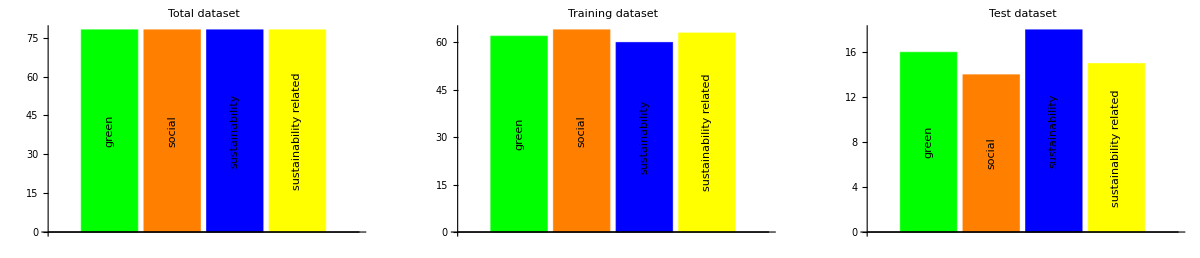

```mathematica
(* Split into training and test set *)
{nobs, ncol} = Dimensions[FullTextLabeledDataset];
{trainingSet,testSet}=TakeDrop[SeedRandom[1234];RandomSample[FullTextLabeledDataset ],Floor[nobs*0.8]];
(* Count of the total for each set to compare them *)
totalCount = SortBy[Dataset[KeyValueMap[<|"label"->#,"freq"->#2|>&,CountsBy[FullTextLabeledDataset ,"label"]]],"label"];
trainingCount = SortBy[Dataset[KeyValueMap[<|"label"->#,"freq"->#2|>&,CountsBy[trainingSet,"label"]]],"label"];
testCount = SortBy[Dataset[KeyValueMap[<|"label"->#,"freq"->#2|>&,CountsBy[testSet,"label"]]],"label"];
(* Plot the distribution *)
totalChart = BarChart[ Normal @ totalCount[All,"freq"], ChartLabels ->Placed[labelsList,Center, Rotate[#,90Degree]&],ChartStyle->{Green, Orange, Blue, Yellow}, PlotLabel->"Total dataset"];
trainingChart =BarChart[ Normal @ trainingCount[All,"freq"], ChartLabels ->Placed[labelsList,Center, Rotate[#,90Degree]&],ChartStyle->{Green, Orange, Blue, Yellow}, PlotLabel->"Training dataset"];
testChart =BarChart[ Normal @ testCount[All,"freq"], ChartLabels ->Placed[labelsList,Center, Rotate[#,90Degree]&],ChartStyle->{Green, Orange, Blue, Yellow}, PlotLabel->"Test dataset"];
GraphicsRow[{totalChart, trainingChart, testChart}, ImageSize->Full]
```

#### Results

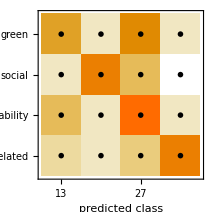
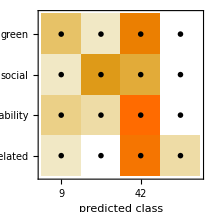
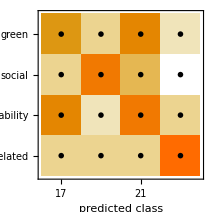
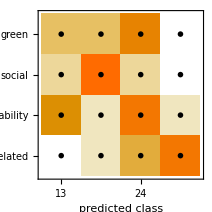
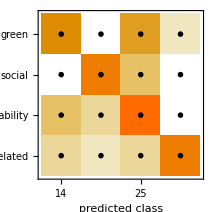
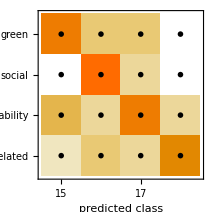
{Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 63
Accuracy | (57.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.312 ± 0.036
Mean cross entropy | 1.17 ± 0.12
Single evaluation time | 57.7 ms/example
Batch evaluation speed | 33. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 63
Accuracy | (41.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.199 ± 0.033
Mean cross entropy | 1.61 ± 0.16
Single evaluation time | 53.3 ms/example
Batch evaluation speed | 33.4 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 63
Accuracy | (49.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.304 ± 0.032
Mean cross entropy | 1.19 ± 0.11
Single evaluation time | 52.1 ms/example
Batch evaluation speed | 32.7 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 63
Accuracy | (51.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.309 ± 0.023
Mean cross entropy | 1.17 ± 0.075
Single evaluation time | 54.7 ms/example
Batch evaluation speed | 33. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (63.6.) %
Accuracy baseline | (29.6.) %
Mean cross entropy | 1050. ± 460.
Single evaluation time | 60.7 ms/example
Batch evaluation speed | 10.4 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NaiveBayes
Number of test examples | 63
Accuracy | (65.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.33 ± 0.073
Mean cross entropy | 1.11 ± 0.22
Single evaluation time | 3.07 s/example
Batch evaluation speed | 1.5 examples/s
-Graphics- | }

```mathematica
(* Trying all the classifiers on the full text. Thereafter, when we mention "Markov" in the results we refer to the "Optimized Markov". For Model 1, Naive Bayes and Optimized Makrov perfomed better in terms of accuracy which was expected as they are both made for text analytics *)
resultsFullText = TryAll[trainingSet,testSet]
```

### Model 2 - Sentences

#### Data preprocessing

```mathematica
(* Function that takes out sentences from the full text and erases sentences containing a url or an email address *)
DivideCleanSentence[pdfPlaintex_]:=DeleteCases[TextSentences[pdfPlaintex],_?(StringContainsQ[#,{"https","www",".com","@"}]&)];
```

```mathematica
(* Apply the function on the training and test sets *)
{SentencetrainingSet,SentencetestSet} = {trainingSet[All,{"text"->DivideCleanSentence}],testSet[All,{"text"->DivideCleanSentence}]};
```

#### Results

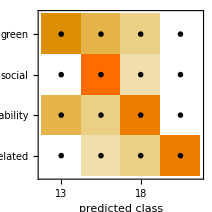
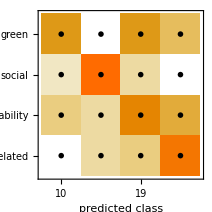
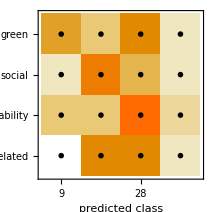
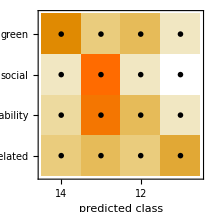
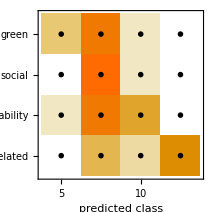
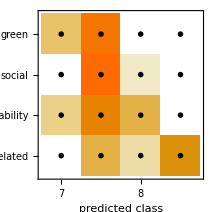
{Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 63
Accuracy | (63.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.265 ± 0.084
Mean cross entropy | 1.33 ± 0.31
Single evaluation time | 18.1 ms/example
Batch evaluation speed | 552. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 63
Accuracy | (56.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.281 ± 0.039
Mean cross entropy | 1.27 ± 0.14
Single evaluation time | 21.2 ms/example
Batch evaluation speed | 510. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 63
Accuracy | (38.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.258 ± 0.018
Mean cross entropy | 1.35 ± 0.068
Single evaluation time | 16.8 ms/example
Batch evaluation speed | 613. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 63
Accuracy | (46.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.279 ± 0.026
Mean cross entropy | 1.28 ± 0.091
Single evaluation time | 20. ms/example
Batch evaluation speed | 523. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (49.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 1.52×10^-33 ± 8.8×10^-14
Mean cross entropy | 75.6 ± 46.
Single evaluation time | 5.35 ms/example
Batch evaluation speed | 413. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NaiveBayes
Number of test examples | 63
Accuracy | (48.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.214 ± 0.066
Mean cross entropy | 1.54 ± 0.3
Single evaluation time | 3.8 s/example
Batch evaluation speed | 1.31 examples/s
-Graphics- | }

```mathematica
(* Apply all the classifiers on the sentences model. Relative to Model 1, when applying our classifiers on average accuracy decreases across the board indicating that maybe using a sentence-based model is not as appropriate *)
TryAll[SentencetrainingSet,SentencetestSet]
```

### Model 3 - Words

#### Data preprocessing

```mathematica
(* Function that takes out words from the full text and erases urls, email addresses and other not encoded characters *)
DivideCleanWords[pdfPlaintex_]:= DeleteCases[TextWords[pdfPlaintex],_?(StringContainsQ[#,{"https","www",".com","@","☐","%","..","©", "☒", "+" ,"ii",".02"}]&)];
```

```mathematica
(* Apply function on the training and test sets *)
{WordstrainingSet,WordstestSet} = {trainingSet[All,{"text"->DivideCleanWords}],testSet[All,{"text"->DivideCleanWords}]};
```

#### First results

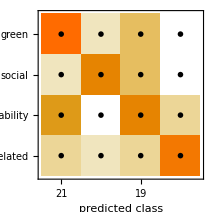
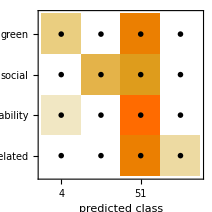
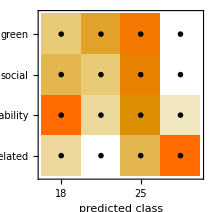
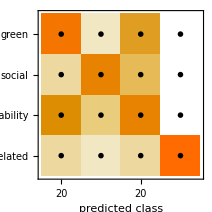
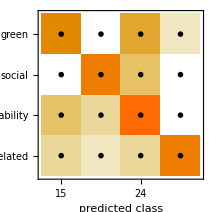
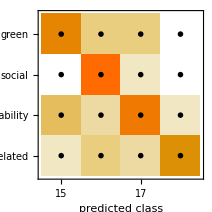
{Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 63
Accuracy | (62.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.189 ± 0.15
Mean cross entropy | 1.66 ± 0.71
Single evaluation time | 38.5 ms/example
Batch evaluation speed | 68.4 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 63
Accuracy | (44.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.192 ± 0.036
Mean cross entropy | 1.65 ± 0.18
Single evaluation time | 32.6 ms/example
Batch evaluation speed | 64.5 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 63
Accuracy | (33.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.245 ± 0.02
Mean cross entropy | 1.41 ± 0.081
Single evaluation time | 47.7 ms/example
Batch evaluation speed | 58.8 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 63
Accuracy | (56.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.351 ± 0.035
Mean cross entropy | 1.05 ± 0.1
Single evaluation time | 43.1 ms/example
Batch evaluation speed | 69.9 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (65.6.) %
Accuracy baseline | (29.6.) %
Mean cross entropy | 1530. ± 830.
Single evaluation time | 58.6 ms/example
Batch evaluation speed | 23. examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NaiveBayes
Number of test examples | 63
Accuracy | (68.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.352 ± 0.071
Mean cross entropy | 1.04 ± 0.2
Single evaluation time | 2.75 s/example
Batch evaluation speed | 1.54 examples/s
-Graphics- | }

```mathematica
(* Apply all the classifiers on the word split model. Similarly to Model 1, Markov-based models seem to perform better in terms of accuracy*)
TryAll[WordstrainingSet,WordstestSet]
```

### Model 4 - Words + SDGs

#### SDG extraction

```mathematica
(* Function that extracts the SDGs contained in the report through a sentences based detection *)
Getsdgs [line_]:= Module[{text=FullTextLabeledDataset[line,"text"]},Select[DeleteDuplicates[Map[StringCases[TextSentences[text][[#]],DigitCharacter..]&,Position[Map[MatchQ[StringPosition[text, "sdg"][[#]],{}]&,Range[Length[StringPosition[text, "sdg"]]]], False]//Flatten]//Flatten]// ToExpression,0<#<18&]]
```

```mathematica
(* Apply the SDGs extraction function*)
DatasetSdgs = FullTextLabeledDataset//Transpose//Append["sdgs"->Map[Getsdgs[#]&,Range[Length[FullTextLabeledDataset]]]]//Transpose;
```

```mathematica
(* Dummify the SDGs variables *)
For[sdgNumber =1,sdgNumber<18,sdgNumber++,DatasetSdgs =DatasetSdgs[All,Append[#,StringJoin["sdg",ToString[sdgNumber]]->If[MemberQ[#sdgs,sdgNumber],1,0]]&]]
DatasetSdgs[1;;2,All]
```

#### Word split

```mathematica
(* Get again the word split since the SDGs exctraction works on the full text and divide into training and test set because the function works on the whole dataset *)
DatasetSdgsWords = DatasetSdgs[All,{"text"->DivideCleanWords}];
(* Add a specific random seed to get the same split as before *)
{trainingSetSDG,testSetSDG}=TakeDrop[SeedRandom[1234];RandomSample[DatasetSdgsWords[All, Drop[DatasetSdgs[[1,All]]//Keys//Normal, {3}]]],Floor[nobs*0.8]];
(* Example of the result *)
trainingSetSDG[1;;6,All]
```

Dataset[<>]

#### Words + SDGs results

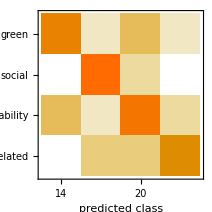
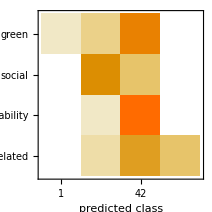
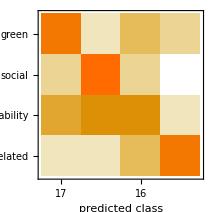
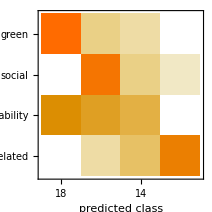
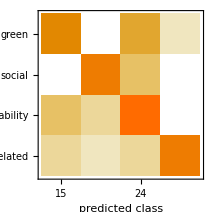
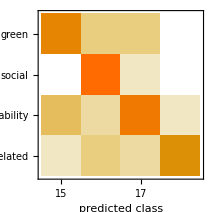
{Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 63
Accuracy | (67.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.0106 ± 0.017
Mean cross entropy | 4.55 ± 1.3
Single evaluation time | 61.9 ms/example
Batch evaluation speed | 57.1 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 63
Accuracy | (51.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.192 ± 0.031
Mean cross entropy | 1.65 ± 0.16
Single evaluation time | 76. ms/example
Batch evaluation speed | 54.9 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 63
Accuracy | (54.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.294 ± 0.025
Mean cross entropy | 1.22 ± 0.084
Single evaluation time | 65.7 ms/example
Batch evaluation speed | 44.4 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 63
Accuracy | (56.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.33 ± 0.031
Mean cross entropy | 1.11 ± 0.095
Single evaluation time | 86.4 ms/example
Batch evaluation speed | 58.4 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (65.6.) %
Accuracy baseline | (29.6.) %
Mean cross entropy | 1530. ± 830.
Single evaluation time | 137. ms/example
Batch evaluation speed | 15.3 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NaiveBayes
Number of test examples | 63
Accuracy | (68.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.353 ± 0.071
Mean cross entropy | 1.04 ± 0.2
Single evaluation time | 3.02 s/example
Batch evaluation speed | 1.29 examples/s
-Graphics- | }

```mathematica
(* Apply all the classification methods on the Words+SDGs model. Similar result as before for Markov-based methods, but also increase on average in accuracy for other methods*)
TryAll[trainingSetSDG,testSetSDG]
```

### Model 5 - Words Optimized

#### Further cleaning

```mathematica
(* Function that deletes words not useful (numbers and one or two letters words) *)
DeepCleaning[text_] := Select[DeleteCases[text//Normal,_?(StringContainsQ[#,ToString/@Range[0,9]]&)],StringLength[#]>2&](*//WordStem*)
```

```mathematica
(* Apply function on training and test set *)
{SDGtrainingSet,SDGtestSet} = {trainingSetSDG[All,{"text"->DeepCleaning}][All,{"text", "label"}],testSetSDG[All,{"text"->DeepCleaning}][All,{"text", "label"}]};
(* Add a new variable that counts specific words *)
newWordsTraining = SDGtrainingSet[All,Append[#,"green count"->Count[#text, "green"]]&];
newWordsTraining = newWordsTraining[All,Append[#,"social count"->Count[#text, "social"]]&];
newWordsTraining = newWordsTraining[All,Append[#,"sustainability count"->Count[#text, "sustainability"]]&];
newWordsTraining = newWordsTraining[All,Append[#,"agriculture count"->Count[#text, "agriculture"]]&];
newWordsTraining = newWordsTraining[All,Append[#,"forestry count"->Count[#text, "forestry"]]&];

newWordsTest = SDGtestSet[All,Append[#,"green count"->Count[#text, "green"]]&];
newWordsTest= newWordsTest [All,Append[#,"social count"->Count[#text, "social"]]&];
newWordsTest = newWordsTest[All,Append[#,"sustainability count"->Count[#text, "sustainability"]]&];
newWordsTest = newWordsTest[All,Append[#,"agriculture count"->Count[#text, "agriculture"]]&];
newWordsTest = newWordsTest[All,Append[#,"forestry count"->Count[#text, "forestry"]]&];
```

#### New results

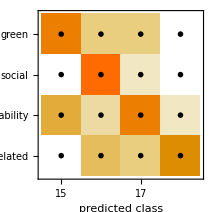
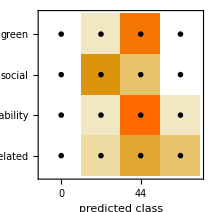
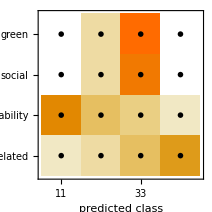
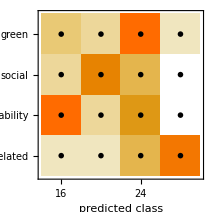
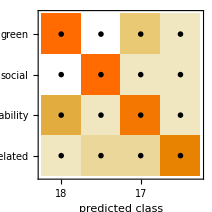
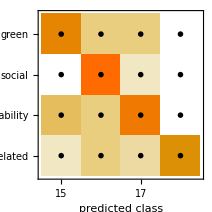
{Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 63
Accuracy | (65.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.361 ± 0.065
Mean cross entropy | 1.02 ± 0.18
Single evaluation time | 20.3 ms/example
Batch evaluation speed | 64.5 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NearestNeighbors
Number of test examples | 63
Accuracy | (48.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.195 ± 0.034
Mean cross entropy | 1.64 ± 0.17
Single evaluation time | 71.6 ms/example
Batch evaluation speed | 57.8 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | DecisionTree
Number of test examples | 63
Accuracy | (21.5.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.157 ± 0.015
Mean cross entropy | 1.85 ± 0.098
Single evaluation time | 20.1 ms/example
Batch evaluation speed | 60.2 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | RandomForest
Number of test examples | 63
Accuracy | (41.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.239 ± 0.035
Mean cross entropy | 1.43 ± 0.15
Single evaluation time | 89.3 ms/example
Batch evaluation speed | 43.4 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | Markov
Number of test examples | 63
Accuracy | (71.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0
Mean cross entropy | 2200. ± 1400.
Single evaluation time | 172. ms/example
Batch evaluation speed | 13.3 examples/s
-Graphics- | ,Classifier Measurements
Classifier method | NaiveBayes
Number of test examples | 63
Accuracy | (68.6.) %
Accuracy baseline | (29.6.) %
Geometric mean of probabilities | 0.351 ± 0.074
Mean cross entropy | 1.05 ± 0.21
Single evaluation time | 2.44 s/example
Batch evaluation speed | 1.87 examples/s
-Graphics- | }

```mathematica
(* Apply all the classification methods with the new model. Good accuracy level - 71 percent with optimised Markov*)
TryAllOpt[newWordsTraining,newWordsTest]
```

### Model 6 - NetModel

```mathematica
(* Import pre-trained word embedding algorithm *)
Glove = NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data"];
(* Create association for the purpose of neural network application *)
associationTraining = AssociationThread[Normal[trainingSet[All,{"text"->Glove}][All,"text"]]->Normal[trainingSet[All, "label"]]]//Normal;
associationTest = AssociationThread[Normal[testSet[All,{"text"->Glove}][All,"text"]]->Normal[testSet[All, "label"]]]//Normal;
(* Add layers to our neural network *)
NetClassifier = 
 NetChain[{DropoutLayer[], NetMapOperator[4], 
   AggregationLayer[Max, 1], SoftmaxLayer[]},
  "Output" -> NetDecoder[{"Class", labelsList}]]
```

NetChain[<>]

```mathematica
(* Train our model *)
trainedModel = NetTrain[NetClassifier, associationTraining , MaxTrainingRounds->600]
```

NetChain[<>]

```mathematica
(* Get accuracy of Neural Network on the full text model *)
NetResults = {NetMeasurements[trainedModel,associationTest,"Accuracy"], None, None, None, None}
```

{0.587302,None,None,None,None}

## First Discussion

After trying numerous machine learning techniques on different models, we can notice that Markov gives the highest accuracy (71%) when applied on the Optimized Words Model (see Table below). This could be explained by the fact that Markov it is explicitly made for text analysis. More in general, we can also conclude that Markov and Naive Bayes tend to give highest accuracy, indeed they are very similar classification methods.  Interestingly, adding SDGs increases the accuracy compared to only words. This could be explained by the fact that certain SDGs tend to belong to one Principle (e.g. Climate Action to Green Bonds). However, this increase was not expected because for many SDGs there is not clear distinction to which Principle they help (e.g., Sustainable Cities and Communities). Finally, the NetModel should be further investigated with different NetModel such as BERT and different NetChain structures to improve its performances.

```mathematica
(* Table with accuracy for each combination of methods *)
columns = {"Full Text", "Sentences", "Words","Words + SDGS", "Optimized Words"};
resultsDataset = AssociationThread[columns->LogisticRegResults]//Dataset;
resultsDataset = Dataset[KeyValueMap[<|"Model"->#,"Logistic Regression"->#2|>&,resultsDataset]];
resultsDataset = resultsDataset //Transpose//Append["KNN"->KNNResults]//Transpose;
resultsDataset = resultsDataset //Transpose//Append["DecisionTree"->DecisionTreeResults]//Transpose;
resultsDataset = resultsDataset //Transpose//Append["RandomForest"->RandomForestResults]//Transpose;
resultsDataset = resultsDataset //Transpose//Append["Markov"->MarkovResults]//Transpose;
resultsDataset = resultsDataset //Transpose//Append["NaiveBayes"->BayesResults]//Transpose;
resultsDataset = resultsDataset //Transpose//Append["NetModel"->NetResults]//Transpose
```

```mathematica
(* Overall, the best model is the Markov method with some more cleaning in of words and without SDGs *)
```

```mathematica
(* Retrain best mode on the whole dataset *)
BestDatasetWords= DatasetSdgsWords[All, {"text", "label"}] ;
BestDatasetWords = BestDatasetWords[All,Append[#,"green count"->Count[#text, "green"]]&];
BestDatasetWords = BestDatasetWords[All,Append[#,"social count"->Count[#text, "social"]]&];
BestDatasetWords = BestDatasetWords[All,Append[#,"sustainability count"->Count[#text, "sustainability"]]&];
BestDatasetWords = BestDatasetWords[All,Append[#,"agriculture count"->Count[#text, "agriculture"]]&];
BestDatasetWords = BestDatasetWords[All,Append[#,"forestry count"->Count[#text, "forestry"]]&];
```

```mathematica
BestModel =Classify[BestDatasetWords ->"label",Method->{"Markov", "Order"->3, "MinimumTokenCount"->5},ValidationSet->Automatic, PerformanceGoal->"Quality" ];
```

```mathematica
Information[BestModel]
```

Classifier information
Data type | Mixed (number: 6)
Classes | ,,greensocialsustainabilitysustainability related
Accuracy | (75.8.) %
Method | Markov
Single evaluation time | 72.7 ms/example
Batch evaluation speed | 16.8 examples/s
Loss | 678. ± 350.
Model memory | 5.73 MB
Training examples used | 312 examples
Training time | 1 0
 |

```mathematica
(* An example of the output of our best model *)
BestModel[BestDatasetWords[1,DeleteCases[BestDatasetWords[1,All]//Keys//Normal, "label"]], "Probabilities"]//Dataset
```

## Interaction

In this way, investors who decide to invest in bonds related to the world of sustainable finance have a tool that allows them to understand to which bond category their investment belongs most. 
In addition, an interactive dashboard is also provided where investors can indicate the SDGs they care most about, and this will show which bonds meet these criteria. In this way we are able to do sustainable finance education and incentivize investments for a more just and environmentally sustainable transition.

### Back-end

#### Classification

```mathematica
(* Same function that gets SDGs from full text but specific for one single document imported by giving specific path *)
GetsdgsDynamic [pdf_]:= Module[{text=ToLowerCase[Import[pdf, "Plaintext", CharacterEncoding->"ASCII"]]},Select[DeleteDuplicates[Map[StringCases[TextSentences[text][[#]],DigitCharacter..]&,Position[Map[MatchQ[StringPosition[text, "sdg"][[#]],{}]&,Range[Length[StringPosition[text, "sdg"]]]], False]//Flatten]//Flatten]// ToExpression,0<#<18&]]
```

```mathematica
(* Function that gets extraxt words from full text and counts spefici words *)
GetWordsDynamic[pdf_] := Module[{data = Dataset[<|"text"->DivideCleanWords[DeleteStopwords[ToLowerCase[Import[pdf, "Plaintext", CharacterEncoding->"ASCII"]]]]|>]},
data =Join[data//Normal,AssociationThread["green count", Count[data["text"], "green"]]]//Dataset;
data =Join[data//Normal,AssociationThread["social count", Count[data["text"], "social"]]]//Dataset;
data =Join[data//Normal,AssociationThread["sustainability count", Count[data["text"], "sustainability"]]]//Dataset;
data =Join[data//Normal,AssociationThread["agriculture count", Count[data["text"], "agriculture"]]]//Dataset;
data =Join[data//Normal,AssociationThread["forestry count", Count[data["text"], "forestry"]]]//Dataset;
data]
(* Retrieve SDG goals description and their images *)
goals = Import["https://raw.githubusercontent.com/GSA/sdg-nrp-scripts/master/data/source/sdg_goals.csv", "Dataset", HeaderLines->1][All, {"goal", "title"}];
iconsPath = FileNames[All,StringJoin[dir,"SDG Icons 2019_WEB"]];
iconsList = Map[Image[Import[#], ImageSize->50]&, iconsPath];
goals = goals//Transpose//Append["Goal"->iconsList]//Transpose;
(* Function that gives back the specific SDGs from a single report *)
dynamicsdg[f_]:=Sort[goals[GetsdgsDynamic[f]]][All,{"Goal", "title"}]
```

#### Browser

```mathematica
(* This code was run to create the database and export it. In order to save time we can just import the result*)
(*
AllpdfClassification = AssociationThread[labelsList->localpdfPath];
AllpdfClassification  = Map[RandomSample[#,10]&,AllpdfClassification];
TextAndName[label_,textNumber_]:=Dataset[{<|"ID"->StringJoin[label,"_",ToString[textNumber]],  "file name" -> FileNameTake[AllpdfClassification[label][[ textNumber]]],  "text"->ToLowerCase[DeleteStopwords[ImportPlainText[label,textNumber]]], "label"-> label, "sdgs"-> GetsdgsDynamic[AllpdfClassification[label][[ textNumber]]]|>}]
TextAndName["green", 1];
TextAndNameDataset =TextAndName["green",1] ;
For[label =1,label<5,label++,For[textNumber=1,textNumber< Length[AllpdfClassification[labelsList[[label]]]]+1,textNumber++, TextAndNameDataset = Join[TextAndNameDataset, TextAndName[labelsList[[label]], textNumber]]]]
TextAndNameDataset = TextAndNameDataset [2;;All];

Export[StringJoin[dir, "AllBonds_Dataset.csv"], TextAndNameDataset]; 
*)
```

```mathematica
(* Importing the pre-created csv file *)
TextAndNameDataset = Import[StringJoin[dir, "AllBonds_Dataset.csv"], "Dataset", HeaderLines->1][All, {"sdgs"->ToExpression}];
```

```mathematica
(* Function to extract one or more specific SDGs from the dataset *)
MultipleChoice[var_,list_] :=And@@Map[MemberQ[var,#]&,list]
SelectSDG[sdglist_]:=TextAndNameDataset[Select[MultipleChoice[#sdgs,sdglist]&],{"file name","label"}]
SelectSDG[{6,7,9}];
```

```mathematica
(* Function that creates interactive tool *)
InteractiveTable =Manipulate[SelectSDG[Select[#!=0&][{SDG1, SDG2, SDG3, SDG4,SDG5, SDG6,SDG7, SDG8,SDG9, SDG10,SDG11, SDG12,SDG13, SDG14,SDG15, SDG16,SDG17}]], Row[{{SDG1,{0,1}}//Control, {SDG2,{0,2}}//Control,{SDG3,{0,3}}//Control, {SDG4,{0,4}}//Control,{SDG5,{0,5}}//Control, {SDG6,{0,6}}//Control,{SDG7,{0,7}}//Control, {SDG8,{0,8}}//Control, {SDG9,{0,9}}//Control,{SDG10,{0,10}}//Control,{SDG11,{0,11}}//Control,{SDG12,{0,12}}//Control,{SDG13,{0,13}}//Control,{SDG14,{0,14}}//Control,{SDG15,{0,15}}//Control,{SDG16,{0,16}}//Control,{SDG17,{0,17}}//Control}, Spacer[20]],ControlType->Checkbox, ControlPlacement->Top];
```

### Import pdf

```mathematica
Print["Select your file"]
FileNameSetter[Dynamic[f]]
Print["File name: ", Dynamic[FileNameTake[f]]]
```

Select your file

$CellContext`fOpenAll

File name:

```mathematica
Button["Get analysis", {sdgdynamic, probsdynamic} ={dynamicsdg[f],(BestModel[GetWordsDynamic[f], "Probabilities"]//ReverseSort)}]
Dynamic[probsdynamic]
Dynamic[sdgdynamic]
```

Get analysis

### Explorer

```mathematica
InteractiveTable
(* Browse the whole dataset of report looking for one or more specific SDG's *)
```

## Final Discussion

Although this project remains a simple experiment by a group of EPFL students,  the importance that the ICMA Principles have in enhancing sustainable finance represents a substantial incentive to further investigate what has been shown. Machine learning applied to sustainable finance constitute a necessary step in the development of this industry, which is as necessary as it is immature.